```mathematica
k=3
n=8
SymmetricPolynomial[k,{x1,x2,x3,x4}]
```

3

8

x1 x2 x3+x1 x2 x4+x1 x3 x4+x2 x3 x4

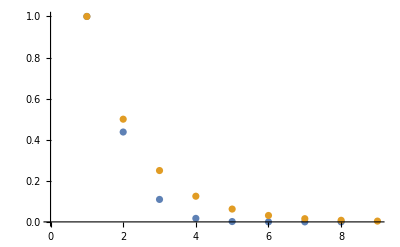

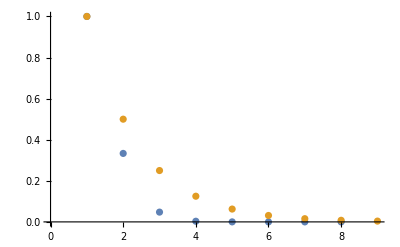

```mathematica
ListPlot[{Table[SymmetricPolynomial[k,{1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8}],{k,1,8}],{1,1/2,1/2^2,1/2^3,1/2^4,1/2^5,1/2^6,1/2^7,1/2^8}}]
ListPlot[{Table[SymmetricPolynomial[k,{1/4,1/2,1/8,1/16,1/32,1/64,1/128,1/128}],{k,1,8}],{1,1/2,1/2^2,1/2^3,1/2^4,1/2^5,1/2^6,1/2^7,1/2^8}}]
```

```mathematica
(*Discrepency only gets worse as n gets large: symmetric functions dominate 2^k*)
```

```mathematica
(*Inner term*)
f[j_] = Sum[(-1)^(k)*2^(k+2)*SymmetricPolynomial[k+2,{1/n,1/n,1/n,1/n,1/n,1/n,1/n,1/n}],{k,j,n-2}]
g[j_] = Sum[(-1)^(k)*SymmetricPolynomial[k+2,{1/n,1/n,1/n,1/n,1/n,1/n,1/n,1/n}],{k,j,n-2}]
gnu[j_] = Sum[(-1)^(k)*SymmetricPolynomial[k+2,{1/4,1/2,1/8,1/16,1/32,1/64,1/128,1/128}],{k,j,n-2}]

Table[f[j],{j,1,6}]
Table[g[j],{j,1,6}]
Table[gnu[j],{j,1,6}]
```

SymmetricPolynomial::nmint: 2+k is not a non-negative machine integer.

∑_(k=j)^6 (-1)^k 2^(2+k) SymmetricPolynomial[2+k,{1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8}]

SymmetricPolynomial::nmint: 2+k is not a non-negative machine integer.

∑_(k=j)^6 (-1)^k SymmetricPolynomial[2+k,{1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8}]

SymmetricPolynomial::nmint: 2+k is not a non-negative machine integer.

∑_(k=j)^6 (-1)^k SymmetricPolynomial[2+k,{1/4,1/2,1/8,1/16,1/32,1/64,1/128,1/128}]

{-42591/65536,14753/65536,-3167/65536,417/65536,-31/65536,1/65536}

{-1575231/16777216,259777/16777216,-26943/16777216,1729/16777216,-63/16777216,1/16777216}

{-1530066917/34359738368,105416731/34359738368,-3433445/34359738368,53467/34359738368,-381/34359738368,1/34359738368}

-3167/65536

-26943/16777216

417/65536

1729/16777216

-31/65536

-63/16777216

1/65536

1/16777216